```mathematica
Quit[]
```

```mathematica
(*  Lewis John Lloyd
	Quiz 02
   Problem 01
	04APR2011
*)
```

-3.25

-195.

{InterpolatingFunction[{{0.,1000.}},<>][t],InterpolatingFunction[{{0.,1000.}},<>][t],InterpolatingFunction[{{0.,1000.}},<>][t]}

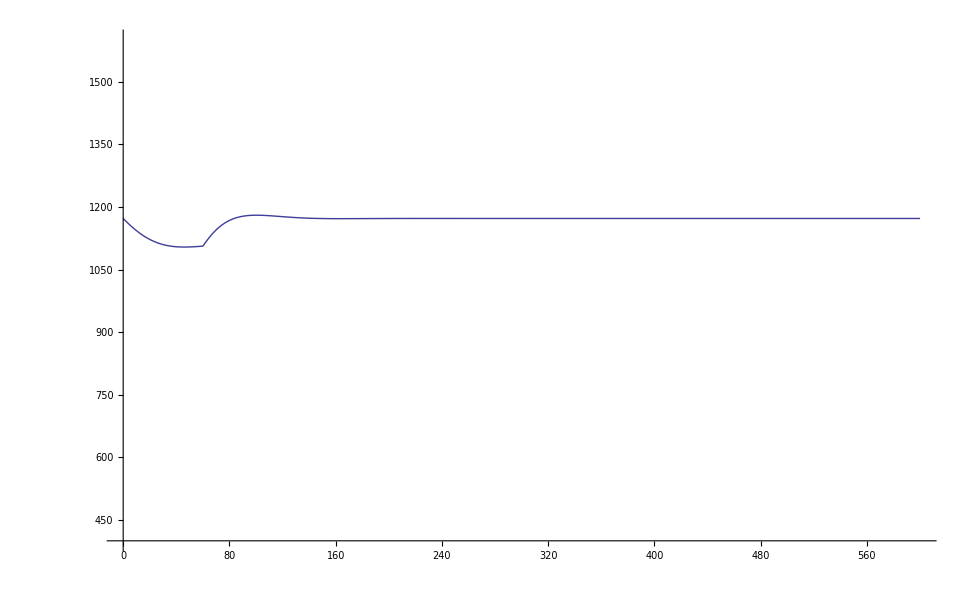

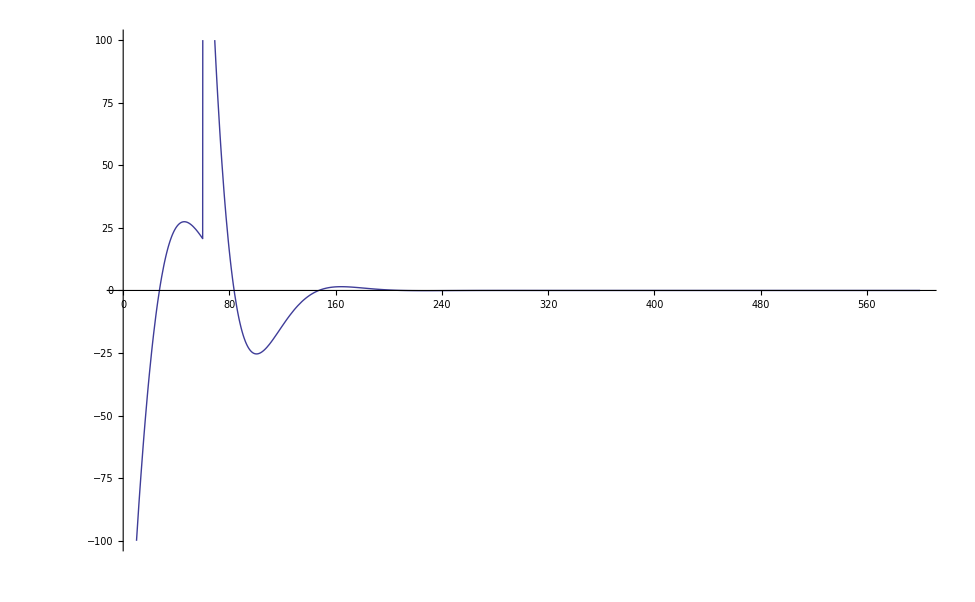

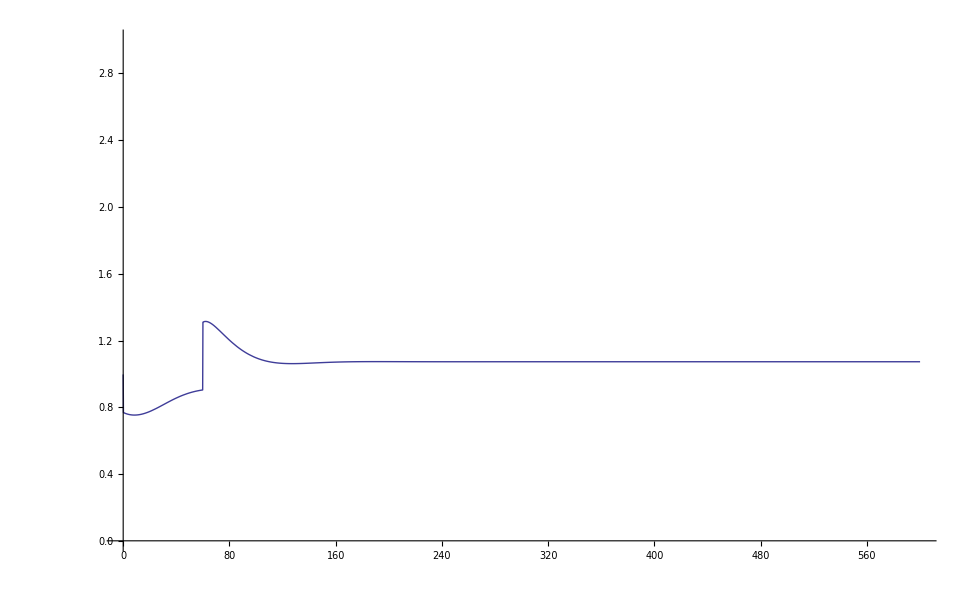

```mathematica
kGraphite=60;(*[W/m-K]*)
SpecificHeatGraphite =710;(* [J/kg-K]*)
DensityGraphite=2267; (*[kg/m^3]*)
DiameterPebble = 0.06; (*[m]*)
DiameterFuel = 0.05; (*[m]*)
RadiusPebble=0.5*DiameterPebble; (*[m]*)
RadiusFuel=0.5*DiameterFuel;(*[m]*)
TemperatureBulk=800;(*[K]*)
HeatTransferCoefficient=500;(*[W/m^2-K]*)
VolumetricHeatSourceInitial=30 10^6;(*[W/m^3]*)
VolumetricHeatSource[t_,r_]=Piecewise[{{
VolumetricHeatSourceInitial(1.5-0.5 ⅇ^(-0.04 t)),0≤ r≤RadiusFuel}}];(*[W/m^3*)
TempInner[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==-VolumetricHeatSourceInitial,T[r],r],C[1]->A0][[1]],C[2]->B0];
TempOuter[r_]=Limit[Limit[T[r]/.DSolve[1/r^2 D[r^2 kGraphite D[T[r],r],r]==0,T[r],r],C[1]->A1][[1]],C[2]->B1];
EquationConstants={A0,A1,B0,B1}/.Solve[{Limit[r^2 TempInner'[r],r->0]==0,
TempInner[RadiusFuel]==TempOuter[RadiusFuel],
-kGraphite TempInner'[RadiusFuel]==-kGraphite TempOuter'[RadiusFuel],
-kGraphite TempOuter'[RadiusPebble]==HeatTransferCoefficient(TempOuter[RadiusPebble]-TemperatureBulk)
},{A0,A1,B0,B1}][[1]]//Expand//Simplify//Chop;
Temperature[r_]=Piecewise[{
{Limit[Limit[TempInner[r],A0->EquationConstants[[1]]],B0->EquationConstants[[3]]],0≤r≤ RadiusFuel},
{Limit[Limit[TempOuter[r],A1->EquationConstants[[2]]],B1->EquationConstants[[4]]],RadiusFuel<r≤RadiusPebble}}];
TemperatureAverage = Integrate[Temperature[r] r^2,{r,0,RadiusPebble}]/Integrate[r^2,{r,0,RadiusPebble}];
VolumePebble = 4/3 π RadiusPebble^3;(*[m^3]*)
VolumeFuel=4/3 π RadiusFuel^3;(*[m^3]*)
SurfacePebble=4π RadiusPebble^2;(*[m^2]*)
CharacteristicRadius=VolumePebble/SurfacePebble;(*[m]*)
BiotPebble =(HeatTransferCoefficient CharacteristicRadius)/kGraphite;(*[-]*)
TauPebble = (HeatTransferCoefficient SurfacePebble)/(DensityGraphite SpecificHeatGraphite VolumePebble); (*[1/s]*) 
1/TauPebble;
ThetaInitial=TemperatureAverage-TemperatureBulk;
lambda={0.0124000000000000,
0.0305000000000000,
0.111000000000000,
0.301000000000000,
1.14000000000000,
3.01000000000000
};
beta={0.000214500000000000,
0.00142350000000000,
0.00127400000000000,
0.00256750000000000,
0.000747500000000000,
0.000273000000000000,
};
β=0.006500000000000;
Λ=7.642722179872736*10^-6;
λ = Sum[beta[[k]],{k,1,6}]/Sum[beta[[k]]/lambda[[k]],{k,1,6}];
α = -β/200;
α*10^5
ρo=-0.3β; 
ρo*10^5
ρ[t_] = ρo(1-HeavisideTheta[t-60])+α(T[t]-ThetaInitial);
{func1[t_],func2[t_],func3[t_]}={PowerLevel[t],T[t],c[t]}/.NDSolve[{
T'[t]==-TauPebble T[t]+(VolumetricHeatSourceInitial*PowerLevel[t]*VolumeFuel)/(DensityGraphite SpecificHeatGraphite VolumePebble),
T[0]==ThetaInitial,
c'[t]==-λ c[t]+β PowerLevel[t],
c[0]==β/λ PowerLevel[0],
 PowerLevel'[t]==((ρ[t]-β)/Λ) PowerLevel[t]+(λ c[t])/Λ,
 PowerLevel[0]==1
},{PowerLevel[t],T[t],c[t]},{t,1000}][[1]]
Plot[func2[t]+TemperatureBulk,{t,0,600},PlotRange->{400,1600}]
Plot[10^5*Limit[ρ[t],T[t]->func2[t]],{t,0,600},PlotRange->{-100,100}]
Plot[func1[t],{t,0,600},PlotRange->{0,3}]
```

```mathematica
func1[900]-func1[0]
func2[900]-func2[0]
func3[900]-func3[0]
```

```mathematica
func2[0]
```

```mathematica
372.54050925925935
```

```mathematica
α*10^5
```

-3.25

```mathematica
0.2β*10^5
```

130.

```mathematica
ρo*10^5
```

-65.

```mathematica
FindRoot[BesselJ[0,x]==0,{x,2}]
```

{x→2.40483}